# CS 465

## Scott Leland Crossen

## Hash Attack Project

### Module

```mathematica
trialData={6,8,10,12,14,16,18,20};
collisionData={23,32,67,100,156,240,401,710};
preimageData={52.14,230.48,1329.22,4747.22,17594.18,68895.34,217189.42,871799.55};
collisionExpected=Fit[Transpose[{trialData, collisionData}],{1, 2^(n/2)},n];
preimageExpected=Fit[Transpose[{trialData, preimageData}],{1, 2^n},n];
tableData=Transpose[{Prepend[trialData, Style["Bit Size",FontSize->18, Bold]],Prepend[ collisionData,Style["Collision Time",FontSize->18, Bold]], Prepend[preimageData,Style["Preimage Time",FontSize->18, Bold]]}];
attackTable=Grid[tableData,
Background->{None,{GrayLevel[0.9],{White}}},
Dividers->{Black,{2->Black}},
Frame->True,
Spacings->{2,{2,{0.7},2}}
];
collisionAttackPlot=Show[
ListPlot[Transpose[{trialData, collisionData}],
AxesLabel->{Style["Bit Size", Black],Style["Attack Time (Attempts)", Black]},
LabelStyle->{Black,  FontSize->18},
PlotLabel->Style["Collision Attack", Black], 
PlotStyle->{Red},
PlotMarkers-> {●,10},
PlotLegends->{"Actual Time"},
PlotRange->All,
ImageSize->450
],
Plot[collisionExpected, {n, 0, Max[trialData] 1.2},
PlotStyle->{Blue},
PlotLegends->{"Predicted Time"},
LabelStyle->{Black,  FontSize->18}
]
];
preimageAttackPlot=Show[
ListPlot[Transpose[{trialData, preimageData}],
AxesLabel->{Style["Bit Size", Black],Style["Attack Time (Attempts)", Black]},
LabelStyle->{Black,  FontSize->18},
PlotLabel->Style["Pre-image Attack", Black], 
PlotStyle->{Red},
PlotMarkers-> {●,10},
PlotLegends->{"Actual Time"},
PlotRange->All,
ImageSize->450
],
Plot[preimageExpected, {n, 0, Max[trialData] 1.2},
PlotStyle->{Blue},
PlotLegends->{"Predicted Time"},
LabelStyle->{Black,  FontSize->18}
]
];
collisionAttackLogPlot = Show[
ListLogPlot[Transpose[{trialData, collisionData}],
AxesLabel->{Style["Bit Size", Black],Style["Attack Time (Attempts)", Black]},
LabelStyle->{Black,  FontSize->18},
PlotLabel->Style["Collision Attack (Log)", Black], 
PlotStyle->{Red},
PlotMarkers-> {●,10},
PlotLegends->{"Actual Time"},
PlotRange->All,
ImageSize->450
],
LogPlot[collisionExpected, {n, 0, Max[trialData] 1.2},
PlotStyle->{Blue},
PlotLegends->{"Predicted Time"},
LabelStyle->{Black,  FontSize->18}
]
];
preimageAttackLogPlot=Show[
ListLogPlot[Transpose[{trialData, preimageData}],
AxesLabel->{Style["Bit Size", Black],Style["Attack Time (Attempts)", Black]},
LabelStyle->{Black,  FontSize->18},
PlotLabel->Style["Pre-image Attack (Log)", Black], 
PlotStyle->{Red},
PlotMarkers-> {●,10},
PlotLegends->{"Actual Time"},
PlotRange->All,
ImageSize->450
],
LogPlot[preimageExpected, {n, 0, Max[trialData] 1.2},
PlotStyle->{Blue},
PlotLegends->{"Predicted Time"},
LabelStyle->{Black,  FontSize->18}
]
];
```

### Introduction

This project is designed to test the efficacy of certain attacks against the SHA-1 hash. Two attacks will be tested: A hashing collision and a hashing pre-image attack. A collision attack is when two sources hash to the same value. A pre-image attack is when a separate source is found that hashes to the same value as a given hash. The first attack runs with complexity O(2^(n/2)) and the second attack runs at complexity O(2^n) where n is the length of the digest in bits.

### Methods and Procedures

To start, a simple wrapper was built around SHA-1 that would take as input a string and produce a truncated hash according to a parameterized length passed into the wrapper. With this function, the complexity of various hash attacks can be analyzed as digest length increases. A series of tests were performed and compared with theoretical models for the attacks as bit size increases. Bit sizes of 6, 8, 10, 12, 14, 16, 18, and 20 were used. Each bit size was ran over 50 trials. The average amount of attempts to produce a hash equal to the given hash (preimage) or previous hash (collision) were then recorded. The average over all 50 trials was calculated and the results were stored for later display in this report. For the pre-image attack, images were pre-calculated using a pool over every possible random combination of strings. The list of pre-images were randomized every trial. After running every attack 50 times for all 8 bit sizes, results were then printed. The script was written in JavaScript.

### Results and Analysis

Below is the raw data showing how many attempts it took to produce a viable collision or preimage of a hash. The rightmost two columns are in units of ‘attempts’. These values did change according to assay but much of the variance was reduced by repeating the experiment over 50 trials. Still, lower bit-sizes produced widely varying results and this was most apparently seen in the log plots included under the appendix.

```mathematica
attackTable
```

Bit Size | Collision Time | Preimage Time
6 | 23 | 52.14
8 | 32 | 230.48
10 | 67 | 1329.22
12 | 100 | 4747.22
14 | 156 | 17594.2
16 | 240 | 68895.3
18 | 401 | 217189.
20 | 710 | 871800.

Notice that the pre-image attack grows much more quickly according to bit size. This is to be expected and is explained in the methods and procedures heading. Below is a comparison of the time it takes to produce a collision and the expected theoretical time plotted alongside. Notice that there is a very good fit for the bit-sizes tested. A theoretical model matching Big-O formalism was fitted to the complexity of O(2^(n/2)). A log-plot is also included for reference in the appendix.

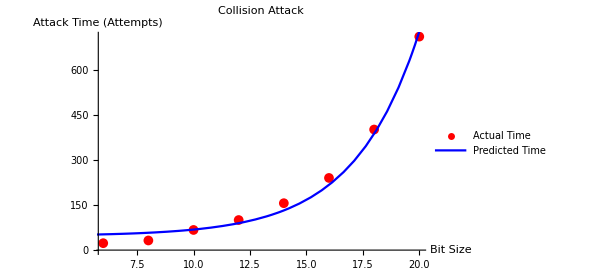

```mathematica
collisionAttackPlot
```

Like the collision attack, the pre-image attack is plotted with it’s theoretical counterpart. It’s theoretical curve was produced using a regression matching the complexity of O(2^n). A log-plot is included for reference in the appendix.

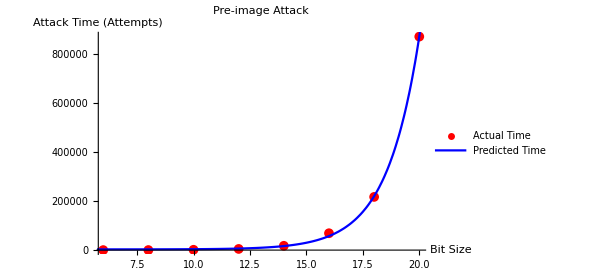

```mathematica
preimageAttackPlot
```

### Conclusion

The conclusion of this report is that the experimental results generally adhere to the theoretical predictions for the given attack. The fit is not perfect, however, and this is can be seen in the log plots for each attack. The collision attack grows at a rate of O(2^(n/2)) and the pre-image attack grows at a rate of O(2^n) where n is the size in bits. As mentioned previously, the complexity of the pre-image attack is higher than that of the collision attack because the hashing algorithm is non-reversible and it takes longer to find a specific hash rather than a previous hash.

### Reviewer

Eddie Crossen

### Appendix

Below are the log plots for the complexity of each attack

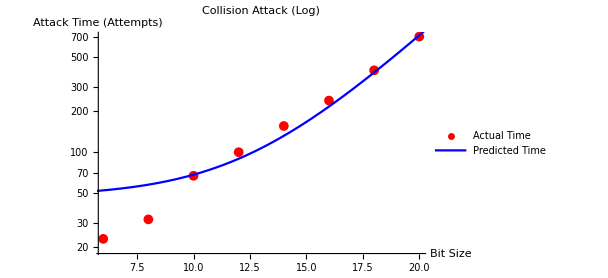

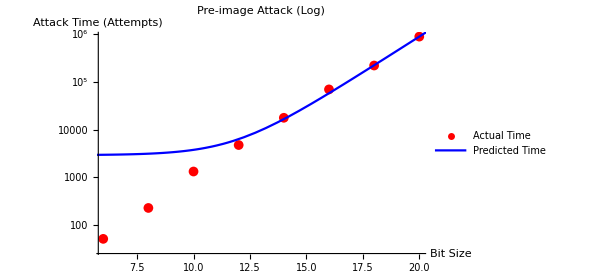

```mathematica
collisionAttackLogPlot
preimageAttackLogPlot
```